```mathematica
Clear["Global`*"]
```

```mathematica
(*batch import*)
file=FileNames["*.png","C:\\Users\\PC\\Desktop\\final year project\\pictures"];
rawPicture=Import[#]&/@file
```

{-Graphics-}

```mathematica
(*initialize*)
massCenter=Table[0,{i,1,Length[rawPicture]}];
edgeCenter=Table[0,{i,1,Length[rawPicture]}];
Do[
(*get grayscale data*)
grayPicture=ColorConvert[rawPicture[[k]],"Grayscale"];
grayData=ImageData[grayPicture];
(*remove background*)
boundary=Mean[Flatten[grayData]]+0.9*StandardDeviation[Flatten[grayData]];
replacementRule=c_/;c<boundary->0;
removeBackgroundData=grayData/.replacementRule;
(*get mass center position*)
massCenterX=Sum[j*removeBackgroundData[[i]][[j]],{i,1,100},{j,1,100}]/Total[Flatten[removeBackgroundData]];
massCenterY=Sum[i*removeBackgroundData[[i]][[j]],{i,1,100},{j,1,100}]/Total[Flatten[removeBackgroundData]];
massCenter[[k]]={massCenterX,massCenterY};
Print["The position of mass center:",massCenter[[k]]];
(*get edge center position*)
horizontalBrightIndex=Flatten[Table[Position[removeBackgroundData[[i]],x_/;x>0],{i,1,Length[removeBackgroundData]}]];
verticalBrightIndex=Flatten[Table[Position[Transpose[removeBackgroundData][[i]],x_/;x>0],{i,1,Length[Transpose[removeBackgroundData]]}]];
edgeCenter[[k]]={Mean[{Max[verticalBrightIndex],Min[verticalBrightIndex]}],Mean[{Max[horizontalBrightIndex],Min[horizontalBrightIndex]}]};
Print["The position of edge center:",edgeCenter[[k]]];
(*show comparison picture*)
removeBackgroundImage=Image[removeBackgroundData,ImageSize->Medium];
Print[Labeled[Show[removeBackgroundImage,Graphics[{Red,Point[{massCenter[[k]][[1]],100-massCenter[[k]][[2]]}]}],Graphics[{Yellow,Point[{edgeCenter[[k]][[1]],100-edgeCenter[[k]][[2]]}]}]],PointLegend[{Red,Yellow},Style[#,18,FontFamily->"Times New Roman"]&/@{"mass center","edge center"}],Right]];
,{k,1,Length[rawPicture]}];
```

The position of mass center:{53.8314,48.3662}

The position of edge center:{50,52}

-Graphics-

```mathematica
(*radial plot*)
radialData=Flatten[Table[{Floor[EuclideanDistance[{i,j},massCenter[[1]]]*4]/4,grayData[[i,j]]},{i,1,100},{j,1,100}],1];
groupedData=SortBy[GroupBy[radialData,First],First];
floorRadialData=Table[Mean[groupedData[[i]]],{i,1,Length[groupedData]}];
radialDataEdge=Flatten[Table[{Floor[EuclideanDistance[{i,j},edgeCenter[[1]]]*4]/4,grayData[[i,j]]},{i,1,100},{j,1,100}],1];
groupedDataEdge=SortBy[GroupBy[radialDataEdge,First],First];
floorRadialDataEdge=Table[Mean[groupedDataEdge[[i]]],{i,1,Length[groupedDataEdge]}];
```

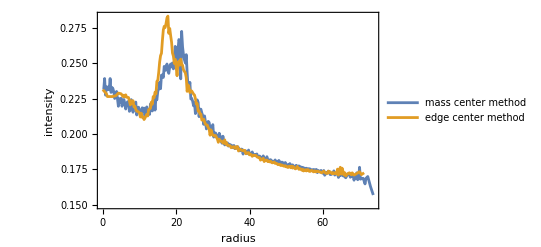

```mathematica
ListLinePlot[{floorRadialData,floorRadialDataEdge},PlotLegends->{Style[#,FontFamily->"Times New Roman",15]&/@{"mass center method","edge center method"}},Frame->True,FrameLabel->{Style["radius",15,FontFamily->"Times New Roman"],Style["intensity",15,FontFamily->"Times New Roman"]},PlotRange->All]
```

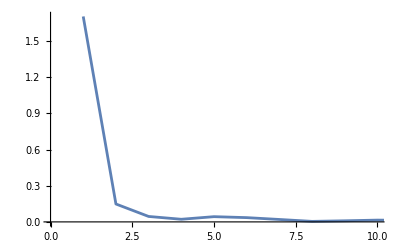

```mathematica
ListLinePlot[Abs[Fourier[Transpose[floorRadialDataEdge][[2]]]],PlotRange->{{0,10},All}]
```

```mathematica
grayDataF=Abs[Fourier[grayData]];
mask=Table[Piecewise[{{1,Abs[50.5-i]>#&&Abs[50.5-j]>#},{0,Abs[50.5-i]<#&&Abs[50.5-j]<#}}],{i,1,100},{j,1,100}]&[30];
rebuildDataF=Abs[InverseFourier[Fourier[grayData]*mask]];
{Image[rawPicture[[1]],ImageSize->Medium],Image[rebuildDataF,ImageSize->Medium]}
```

{-Graphics-,-Graphics-}

```mathematica
Image@grayDataF
```

-Graphics-

```mathematica
testData=Abs[Fourier[grayData]];
len=Length[testData];
Image@Flatten[{Transpose@Join[Transpose@#3[#3[testData[[#1,#1]],1],2],Transpose@#3[#3[testData[[#1,#2]],1],2]]&[1;;len/2,len/2+1;;len,Reverse],Transpose@Join[Transpose@#3[#3[testData[[#2,#1]],1],2],Transpose@#3[#3[testData[[#2,#2]],1],2]]&[1;;len/2,len/2+1;;len,Reverse]}&[1;;len/2,len/2+1;;len,Reverse],1]
```

-Graphics-

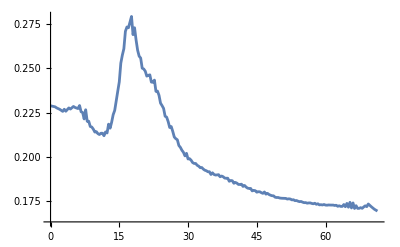

```mathematica
radialDataF=Flatten[Table[{Floor[EuclideanDistance[{i,j},edgeCenter[[1]]]*#]/#,rebuildDataF[[i,j]]},{i,1,100},{j,1,100}],1]&[3];
groupedDataF=SortBy[GroupBy[radialDataF,First],First];
floorRadialDataF=Table[Mean[groupedDataF[[i]]],{i,1,Length[groupedDataF]}];
ListLinePlot[floorRadialDataF,PlotRange->All]
```